### Simplified version of the notebook by Martin Zand et al. https://www.mathematica-journal.com/2015/09/30/graphical-representation-of-proximity-measures-for-multidimensional-data/

For the sake of brevity, the datasets are placed here in collapsed cells, along with several housekeeping functions for displaying tables and figures. Some of the data for intra-airport distances is retrieved by using the AirportData function and requires internet access if executing the notebook again.

```mathematica
airLabsI={"Atlanta","Billings","Birmingham","Bismark","Boise","Boston","Buffalo","Chicago","Cleveland","Dallas","Denver","Des Moines","Detroit","El Paso","Houston","Indianapolis","Kansas City","Little Rock","Los Angeles","Louisville","Memphis","Miami","Minneapolis","New Orleans","New York","Omaha","Philadelphia","Phoenix","Pittsburgh","Portland","Raleigh-Durham","St. Louis","Salt Lake City","San Francisco","Seattle","Washington"};
airLabsShort={"ATL","BIL","BHM","BIS","BOI","BOS","BUF","ORD","CLE","DFW","DEN","DSM","DTW","ELP","HOU","IND","MCI","LIT","LAX","SDF","MEM","MIA","MSP","MSY","JFK","OMA","PHL","PHX","PIT","PDX","RDU","STL","SLC","SFO","SEA","DCA"};
airLabs=Table[(airLabsI[[i]]<>" ("<>airLabsShort[[i]]<>") "),{i,Length[airLabsShort]}];
geoCoordsAir=airGeo=AirportData[#,"Coordinates"]&/@ airLabsShort;
airData=Table[Round[GeoDistance[airGeo[[i]],airGeo[[j]]]][[1]],{i,1,Length[airGeo]},{j,1,Length[airGeo]}];
```

```mathematica
ScrollTable[data_,xlabs_,ylabs_,size_:{500,300},sbars_:{True,True}]:=Column[{Pane[Style[TableForm[data,TableAlignments->{Right,Bottom},TableHeadings->{ylabs,Rotate[#,-Pi/2]&/@xlabs}],8,FontFamily->"Arial", Bold],size,Scrollbars->sbars,ImageSizeAction->"Scrollable"]},Alignment->{Left,Baseline}]
```

```mathematica
TableFigure[data_,xlabs_,ylabs_,size_]:=Column[{Style[TableForm[data,TableAlignments->{Right,Bottom},TableHeadings->{ylabs,xlabs}],size,Bold,FontFamily->"Arial"]},Alignment->Left]
```

```mathematica
ScrollMatrix[data_,size_:{500,300},mtxStyle_:{FontFamily->"Arial",9}]:=Pane[Style[MatrixForm[data],mtxStyle],ImageSize-> size,Scrollbars->True,ImageSizeAction->"Scrollable"]
```

```mathematica
colorbarL[{min_,max_},colorFunction_: Automatic,divs_: 150,title_:"",size_:{200,80}]:=DensityPlot[x,{x,min,max},{y,0,0.1},AspectRatio->.1,PlotRangePadding->0,PlotPoints->{divs,2},MaxRecursion->0,Frame->True,FrameLabel->{{None,None},{title,None}},ImageSize->size,LabelStyle->Directive[FontFamily->"Arial",10, Bold],FrameTicks->{{None,None},{All,None}},FrameTicksStyle->Directive[FontFamily->"Arial",9,Plain],ColorFunction->colorFunction]
```

### 5.2. Case Study: Airport Location Mapping

We begin with one of the original motivating problems related to MDS, reconstructing the relative locations between cities in two dimensions, knowing only the relative distances between each one. We use the United States airport distance data from Section Section and reconstruct the cities’ relative geographic positions. We begin by squaring the distance functions and calculating the scale of the dataset.

```mathematica
Am=airData^2;
scale=Length[Am];
```

Next, we create an identity matrix, with all elements being 0 except the diagonal elements, which are 1, and a constant matrix with all elements equal to 1. Both matrices are of the same dimensions and are used in subsequent calculations to transform data from 28 down to two dimensions.

```mathematica
Idm=IdentityMatrix[Length[Am]];
oneM=ConstantArray[1,Dimensions[Am]];
```

We then calculate the kernel matrix and double-center the new N-dimensional coordinates.

```mathematica
J=Idm-1./scale oneM;
Bm=-1/2 J.Am.J;
```

With the number of dimensions set to 2, the matrix eigenvectors and eigenvalues are calculated. The sign of the first eigenvector is adjusted to lay out the cities from west to east. (Mathematica does not guarantee the direction of an eigenvector.)

```mathematica
dim=2;
Em=Eigenvectors[Bm,dim]If[$VersionNumber<10.2,1,{-1,1}]
```

{{-0.129171,0.164791,-0.101168,0.0843364,0.248814,-0.237447,-0.155102,-0.0613687,-0.128977,0.0244763,0.122908,0.000635832,-0.109603,0.141688,-0.00345098,-0.0865066,0.00785255,-0.0313444,0.291272,-0.0981005,-0.0577967,-0.210212,0.00330048,-0.0674643,-0.218743,0.0249825,-0.207308,0.212435,-0.150431,0.310908,-0.187052,-0.0432586,0.205778,0.33099,0.302226,-0.192888},{-0.138278,0.17658,-0.154413,0.210242,0.117269,0.230394,0.184481,0.0997557,0.116632,-0.218811,-0.0125633,0.0620399,0.131882,-0.267718,-0.314541,0.0380486,-0.0115239,-0.144878,-0.182929,-0.00641343,-0.125285,-0.349034,0.168374,-0.282816,0.154349,0.0477733,0.118949,-0.213395,0.0993995,0.203908,-0.0304331,-0.0120272,0.0201888,-0.0508981,0.262057,0.0736327}}

```mathematica
Ev=Eigenvalues[Bm,dim]
```

{2.14663×10^7,4.77758×10^6}

The transformation matrix dMTX is calculated from a diagonal matrix formed by the eigenvalues Ev, and the coordinate matrix EmM is calculated from the eigenvectors Em.

```mathematica
dMTX=DiagonalMatrix[Ev];
EmM=Transpose[Em];
```

```mathematica
Column[{Style["Transformation Matrix",FontFamily->"Arial",Bold],dMTX//MatrixForm," ",Style["Coordinate Matrix",FontFamily->"Arial",Bold],EmM//MatrixForm},Alignment->Left]
```

Transformation Matrix
(2.14663×10^7 | 0.
0. | 4.77758×10^6)
 
Coordinate Matrix
(-0.129171 | -0.138278
0.164791 | 0.17658
-0.101168 | -0.154413
0.0843364 | 0.210242
0.248814 | 0.117269
-0.237447 | 0.230394
-0.155102 | 0.184481
-0.0613687 | 0.0997557
-0.128977 | 0.116632
0.0244763 | -0.218811
0.122908 | -0.0125633
0.000635832 | 0.0620399
-0.109603 | 0.131882
0.141688 | -0.267718
-0.00345098 | -0.314541
-0.0865066 | 0.0380486
0.00785255 | -0.0115239
-0.0313444 | -0.144878
0.291272 | -0.182929
-0.0981005 | -0.00641343
-0.0577967 | -0.125285
-0.210212 | -0.349034
0.00330048 | 0.168374
-0.0674643 | -0.282816
-0.218743 | 0.154349
0.0249825 | 0.0477733
-0.207308 | 0.118949
0.212435 | -0.213395
-0.150431 | 0.0993995
0.310908 | 0.203908
-0.187052 | -0.0304331
-0.0432586 | -0.0120272
0.205778 | 0.0201888
0.33099 | -0.0508981
0.302226 | 0.262057
-0.192888 | 0.0736327)

The graph coordinates cMDScoord are calculated and projected to two dimensions.

```mathematica
cMDScoord=EmM.√dMTX
```

{{-598.473,-302.244},{763.504,385.964},{-468.731,-337.511},{390.745,459.541},{1152.8,256.323},{-1100.13,503.588},{-718.612,403.233},{-284.332,218.043},{-597.573,254.93},{113.403,-478.27},{569.455,-27.4605},{2.94592,135.605},{-507.808,288.264},{656.464,-585.169},{-15.989,-687.514},{-400.8,83.1654},{36.3822,-25.1885},{-145.224,-316.669},{1349.51,-399.841},{-454.517,-14.0183},{-267.782,-273.843},{-973.947,-762.908},{15.2917,368.028},{-312.574,-618.169},{-1013.47,337.371},{115.748,104.421},{-960.493,259.995},{984.249,-466.433},{-696.974,217.264},{1440.49,445.696},{-866.642,-66.5197},{-200.425,-26.2887},{953.404,44.128},{1533.53,-111.251},{1400.26,572.796},{-893.684,160.944}}

Finally, we plot the two-dimensional airport locations in cMDScoord, which shows the airports in the new coordinate system.

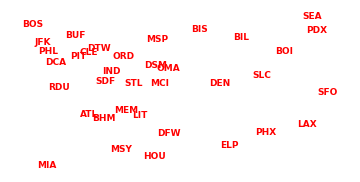

```mathematica
Framed[Graphics[Table[{Text[Style[airLabsShort[[i]],Red,Bold,FontFamily->"Arial",9],cMDScoord[[i]]]},{i,1,Length[cMDScoord]}],ImageSize->Medium],FrameStyle->LightGray]
```

Figure NumberedFigure. Classical MDS display of relative airport locations.

Classical multidimensional scaling gives a solution that has an excellent projection of the cases in a lower dimension, preserving the between-cases distances from N dimensions. It is important to note, however, that the solution is not unique with respect to the rotation and reflection of the visualization. It is often the case when one knows the “true” orientation of the case locations (e.g. the previous map example), that classical (and metric) MDS methods yield a visualization that is reflected or rotated. In these cases, use of other boundary conditions (fixing known coordinates) helps constrain the orientation of the solution. Often, however, such boundary conditions are not available.

Given the above solution, how well does classical MDS reproduce the airport coordinates? Because we have a gold standard, the actual airport locations, comparison of the coordinate estimates is possible. However, the airport locations are represented in a geographic coordinate system, making a comparison of calculated versus actual airport locations a bit more complicated. One approximate way to approach this issue is by first examining the correlation between the actual airport locations, in longitude and latitude coordinates, and the derived coordinates from the classical MDS calculation, using the PearsonCorrelationTest. The units are different, which we will address in a moment, but this does not affect the Pearson correlation test.

```mathematica
TrcMDSCoordinates=cMDScoord;geoCoordsAir=Table[{airGeo[[i,1,2]],airGeo[[i,1,1]]},{i,Length[airGeo]}];

correl=Correlation[geoCoordsAir[[All,#]],TrcMDSCoordinates[[All,#]]]&/@{1,2};

pLabel=Style[Column[{Row[{{"Longitude","Latitude"}[[#]]," versus ", {Style["X",Italic],Style["Y",Italic]}[[#]]}],Row[{Style["r",Italic]," = ",correl[[#]]}]},Center],FontFamily->"Arial",Bold,10,Black]&/@{1,2};

Grid[{Labeled[ListPlot[Table[{geoCoordsAir[[i,#]],TrcMDSCoordinates[[i,#]]},{i,Length[geoCoordsAir]}],Axes->False,Frame->{{True,False},{True,False}},BaseStyle->Directive[FontFamily->"Arial",9],FrameLabel->{{ Column[{"","Metric MDS Coordinates"}]," "},{"True Coordinates",""}},ImageSize->{250,Automatic}],pLabel[[#]],Top]&/@{1,2}}]
```

Part::partd: Part specification {{33.6367,-84.4281},{45.8077,-108.543},{33.5629,-86.7536},{46.7727,-100.746},{43.5644,-116.223},{42.363,-71.0064},{42.9405,-78.7322},{41.9786,-87.9048},{41.4117,-81.8498},«18»,{33.4343,-112.012},{40.4915,-80.2329},{45.5887,-122.598},{35.8776,-78.7875},{38.7487,-90.37},{40.7884,-111.978},{37.619,-122.375},{47.449,-122.309},{38.8521,-77.0377}}⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification {{33.6367,-84.4281},{45.8077,-108.543},{33.5629,-86.7536},{46.7727,-100.746},{43.5644,-116.223},{42.363,-71.0064},{42.9405,-78.7322},{41.9786,-87.9048},{41.4117,-81.8498},«18»,{33.4343,-112.012},{40.4915,-80.2329},{45.5887,-122.598},{35.8776,-78.7875},{38.7487,-90.37},{40.7884,-111.978},{37.619,-122.375},{47.449,-122.309},{38.8521,-77.0377}}⟦1,1,1⟧ is longer than depth of object.

Part::partd: Part specification {{33.6367,-84.4281},{45.8077,-108.543},{33.5629,-86.7536},{46.7727,-100.746},{43.5644,-116.223},{42.363,-71.0064},{42.9405,-78.7322},{41.9786,-87.9048},{41.4117,-81.8498},«18»,{33.4343,-112.012},{40.4915,-80.2329},{45.5887,-122.598},{35.8776,-78.7875},{38.7487,-90.37},{40.7884,-111.978},{37.619,-122.375},{47.449,-122.309},{38.8521,-77.0377}}⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Figure NumberedFigure. Comparison of actual and estimated coordinates.

While the correlations are high, they are not perfect, as we can see by the off-diagonal locations of some of the points. To better visualize these differences, we transform the classical MDS coordinates into longitude and latitude units. This is a transformation that uses the pseudoinverse matrix to translate and rotate to find a good alignment between the two coordinate sets.

```mathematica
newcoords=Map[#+{c,d}&,TrcMDSCoordinates.{{a,b},{-b,a}}];
{vec,mat}=CoefficientArrays[Flatten[newcoords],{a,b,c,d}];
res=Thread[{a,b,c,d}->PseudoInverse[mat].Flatten[geoCoordsAir]]
```

This type of transformation preserves the relative distances between the classical MDS derived city locations and thus provides a relatively accurate estimate of how close the estimates are to the actual city locations. A more accurate solution would involve mapping of the coordinates to an appropriate spherical projection system; however, this is outside the focus of this article.

The transformation coefficients can now be used to transform the classical MDS derived coordinates into GeoPosition values. To compare the actual (●) with the cMDS calculated (◆) airport locations, we use the GeoListPlot function, which plots both sets of points on a map of North America.

```mathematica
transCMDS=newcoords/.res;
geoMMDS=Map[GeoPosition,Map[Reverse,transCMDS]];
```

```mathematica
GeoListPlot[{airGeo,geoMMDS},PlotStyle->{Black,Red},PlotLegends->{"Actual","cMDS"},ImageSize->{350,Automatic}]
```

-Graphics-

Figure NumberedFigure. Comparison of airport geo locations.

The accuracy of the classical MDS estimates is fairly good, but not perfect. Part of this error is due to the approximate transformation from arbitrary MDS coordinates to geographic coordinates, and the complex projection to a flat map.